Reading Analog Clocks and Gauges

Sanchez Santiago

Daily Kevin

EAFIT University

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: Being able to teach a computer to read analog clocks or gauges as a solution for monitoring old machinery, non electrical equipment like gas tanks or even for people with visual disabilities.

SUMMARY OF WORK: 
●  First Goal → Reading a gauge
  •  Approach Method: 
     ·  Train a Predict model (Method→”NearestNeighbors”)  with 3000 gauges of 8 different types.
  +• Challenges: Ranges and kinds of gauges can vary too much.
  +• Solution: Setting one specific kind of gauge and display the range as a percentage to be fitted to any range.
● Second Goal → Reading a clock
  •  Approach Method: 
     · Extract the arms of the clock using the “Hough Transform” feature extraction technique.
     · Make a rotating mask over the clock’s image counting the number of pixels in every angle of the mask. 
     · Train a Predict model  (Method→”NearestNeighbors”) with 10.000 clocks of 6 different types.       
  +• Challenges: Three arms and the symmetry ,of clocks were the difficult to overcome.
  +• Solution: An specific image processing and a big amount of training data.

RESULTS AND FUTURE  WORK: 
● Results
   First Goal → 98% of accuracy on randomly generated data.
    Second Goal → 86% of accuracy on randomly generated data.
● Future Work
In both of the goals the data used was generated by WL functions, some random images from internet were used giving less accurate results, is necessary to train the machine learning algorithm with real labeled images for using it in real applications.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

### Demonstration

```mathematica
DynamicModule[{gaugeGraphic,val=RandomReal[],int=1,makeGauge,gaugeThemes,pG,clockThemes,k=Flatten[Table[{i,j},{i,1,12},{j,1,60}],1],pC,hour=1,min=1,int2=1,im3,im4,clockGraphic,clockValues},

Panel@Row[{
Grid[
{
{Button["Randomize",
val=RandomReal[];
int=RandomInteger[{1,8}];
gaugeGraphic=makeGauge[val,int];
]},
{Dynamic[gaugeGraphic]}
}
],

Spacer[20],

Grid[
{
{Button["Randomize",
hour=RandomInteger[{1,12}];
min=RandomInteger[{1,60}];
int2=RandomInteger[{1,6}];
clockGraphic=im4[hour,min,int2];
clockValues=k[[pC[im3[hour,min,int2]]]];
]
},
{
Row[{
Dynamic[clockGraphic],
Spacer[10],
Dynamic@Grid[{{"Hour","Minute"},clockValues}]
}]
}
}
]
}],
Initialization:>(
gaugeThemes={"Business","Detailed","Marketing","Minimal","Monochrome","Scientific","Web","Classic"};
pG=Import["https://raw.githubusercontent.com/ssanch30/Santiago_Sanchez/master/Gauge_Predict.m"];
makeGauge[v_,int_]:=Module[{},
Row[{
AngularGauge[v,{0,1},PlotTheme->gaugeThemes[[int]]],
Spacer[10],
Column[{
"Value",
pG[ColorConvert[ImageResize[Rasterize[AngularGauge[v,{0,1},PlotTheme->gaugeThemes[[int]]]],{50,50}],"Grayscale"]]
}]
}]
];
gaugeGraphic=makeGauge[val,int];

clockThemes={"Detailed","Minimal","Monochrome","Scientific","Web","Classic"};
pC=Import["https://raw.githubusercontent.com/ssanch30/Santiago_Sanchez/master/MultiClock_Predict.m"];
im3[h_,m_,t_]:=ImageResize[ColorConvert[Rasterize[ClockGauge[{h,m}, PlotTheme->clockThemes[[t]]]],"Grayscale"],{50,50}];
im4[h_,m_,t_]:=ClockGauge[{h,m}, PlotTheme->clockThemes[[t]]];
clockGraphic=im4[hour,min,int2];
clockValues=k[[pC[im3[hour,min,int2]]]];
),
SynchronousInitialization->False
]
```

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

## Introduction

Human’s most powerful sensor is the vision, 2/3 of the cerebral cortex is involved indirectly on computing all of the signals captured by the eyes, that’s maybe why is so difficult to teach a computer to understand what humans see and interpret it as we do, simple task like read an analog clock could be a very challenging task for a machine because what the computer sees is a huge amount of values that correspond to the brightness of each pixel.

Automation is not only required for companies with brand new machines, automation is also required for companies with old machines that have a lot of analog gauges and clocks, these clocks and gauges are only possible to be read by humans because they don’t  have digital nor analog outputs to deliver to a microprocessor, it is also not possible to collect their data for detecting anomalous behavior or prevent damages, only humans are able to know what exactly means and it is worth ti to pay a person to be checking this machines many times in the day.

An algorithm for knowing the scalar value of these clocks and gauges could be a solution for those kinds of companies and also for robotics, that are meant to recognize it’s environment  and to make decisions from the information collected.

#### First Goal → Reading a gauge.

The first attempt to solve this task was to create a large amount of labeled gauges, this data is generated by the function AngularGauge with different kinds of PlotTheme to generate different gauges and be able to predict the result with the Predict function with the Method→ “NearestNeighbor”, other methods were used bur NearestNeighbor was the one with better results.

This attempt didn’t went well straightaway because the size of the image, it was too heavy and it was very time consuming to generate 3000 random gauges. Many image processing function where used to solve this task.

As gauges has so many types it it’s necessary to choose a kind of gauge, circular and about 300.ba,  and make the range from 0 to 1 to be able to multiply it depending of the range of the gauge is meant to be read.

#### Second Goal → Reading a clock.

#### Hough Transform

The same strategy used for the first goal was used on this goal with poor results, of course because of the number of arms. it is used a function called ImageLines which gives as result the next graph.

-Graphics-or "Segmented"-Graphics- 

After it’s segmented it’s necessary to select the strongest and longest ones with the function Position, EuclideanDistace & Part which gives the following result.
-Graphics- the background image can be modified to make more visible the features extracted →

#### Rotative Mask

The rotative mask was an alternative without using machine learning, this alternative works very good on WL generated clocks and only in some of the types of themes, because it works by counting the number of pixels existing in each angle of the mask so if the image has some noise, the results are not going to be corrects.

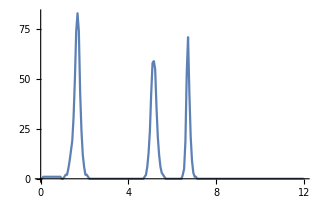
However over an ideal image it performs very well. The count of black pixels with the angle interpreted as the 12 hours, it’s possible to find the peaks on the plot being the higher value the minutes, the second higher are the seconds and the lowest is the hour.

-Graphics-

#### Predict (NearestNeighbor)

The first and the final approach but with lot of knowledge gained, it was possible to generate a data set as small to be able to compute it but as clear to be able to extract the most important features of it.
The training was made over 8000 labeled clock images and tested over 2000 images.

Main Results in Detail

#### Hough Transform

Good approach, the features were extracted correctly but took too much time to compute each so it was not possible to get enough data for a machine learning model.

#### Rotating Mask

This non machine learning approach was very accurate for white back-grounded clocks, but not enough to be able to read different kinds of clocks and very time consuming.

#### Predict

First Goal → 98% of accuracy on randomly generated data over 600 test.

Second Goal → 86% of accuracy on 2000 randomly generated data over 2000 test.

Machine Learning (NearestNeighbor) approach, very accurate, but now it needs to be trained on real world images.

Code

```mathematica
Hyperlink["WSS17: Reading Analog Clocks and Gauges","https://github.com/ssanch30/Santiago_Sanchez"]
```

Written Content / Lesson Plans

Conclusions in Detail

Both of the cases were tested with external data (Internet images), and their performance was not as good as the performance with WL generated data, this is because the data set is biased. It’s necessary to train over a wide number of external labeled images in order to get more accurate results.

The feature extraction “Hough Transform” must be optimized or parallelized because it can extract even the circles from an image making possible to label and use more external data.

All Visualizations

Data Sources Links/References

· https://en.wikipedia.org/wiki/Hough_transform

· Analog clock and watch reader , Chemi Shumacher

Future Directions

Generate a “Clock Detector” able to make a bounding box around the clock or gauge.

Text recognition on the image, sometimes in rotated orientation  to know the range of the gauges.

Background Info Links/References

Keywords

Provide keywords as items

< machine learning  >

< computer vision >

< analog clock >

< ClockGauge >

< AngularGauge >

Other

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```